```mathematica
(* ============================================================*)
(* Y(k1,mu) X-bar(k2) X(k3) -> X-bar(p1) X(p2)              *)
(* 4D, Mandelstam variables, NR applied per-term               *)
(* 8 Feynman diagrams: 4 s-channel + 4 t-channel              *)
(*                                                              *)
(* Relative sign: s-channel (direct) = +1                      *)
(*                t-channel (exchange) = -1                     *)
(* ============================================================*)
<< FeynCalc`
FCClearScalarProducts[];

(* ---Scalar products: 4D Mandelstam-like--- *)
SP[k1, k1] = mY^2; SP[k2, k2] = mX^2;
SP[k3, k3] = mX^2; SP[p1, p1] = mX^2; SP[p2, p2] = mX^2;

SP[k1, k2] = (s12 - mY^2 - mX^2)/2;
SP[k1, k3] = (s13 - mY^2 - mX^2)/2;
SP[k1, p1] = (mY^2 + mX^2 - t1)/2;
SP[k2, p1] = (2 mX^2 - t2)/2;
SP[k3, p1] = (2 mX^2 - t3)/2;

(* k2.k3 from p2^2 = mX^2, using p2 = k1+k2+k3-p1 *)
SP[k2, k3] = -(s12 - mY^2 - mX^2)/2 - (s13 - mY^2 - mX^2)/2
             + (mY^2 + mX^2 - t1)/2 + (2 mX^2 - t2)/2
             + (2 mX^2 - t3)/2 - (mY^2 + 2 mX^2)/2;

(* p2 = k1+k2+k3-p1 cross terms *)
SP[p2, k1] = SP[k1, k1] + SP[k1, k2] + SP[k1, k3] - SP[k1, p1];
SP[p2, k2] = SP[k1, k2] + SP[k2, k2] + SP[k2, k3] - SP[k2, p1];
SP[p2, k3] = SP[k1, k3] + SP[k2, k3] + SP[k3, k3] - SP[k3, p1];
SP[p2, p1] = SP[k1, p1] + SP[k2, p1] + SP[k3, p1] - SP[p1, p1];

(* ---NR definitions--- *)
sqrtsNR = mY + 2 mX;
sNR = sqrtsNR^2;
EXf = sqrtsNR/2;

NRrules = {
   s12 -> (mY + mX)^2,
   s13 -> (mY + mX)^2,
   t1 -> mY^2 + mX^2 - 2 mY EXf,
   t2 -> 2 mX^2 - 2 mX EXf,
   t3 -> 2 mX^2 - 2 mX EXf
};

(* ---Massive Y propagator (numerator)--- *)
YProp[a_, b_, q_] := -MT[a, b]+ FV[q, a] FV[q, b]/mY^2; 

(* ============================================================*)
(* S-CHANNEL (direct) diagrams: signs = +1                     *)
(* Wick contraction: X-bar(k2)<->X(k3) and X-bar(p1)<->X(p2)  *)
(* ============================================================*)

(* ---- S1: incoming s-channel, X-bar(p1) at middle vertex ---- *)
(* v1: X-bar(k2)+X(k3) -> Y*(k2+k3)                           *)
(* v2: Y* -> X-bar(p1) + X_prop                                *)
(* v3: X_prop + Y(k1) -> X(p2)                                 *)
(* X prop: arrow v2->v3, P along arrow = k2+k3-p1              *)
qY1 = k2 + k3;
PX1 = k2 + k3 - p1;
DenY1 = ExpandScalarProduct[SP[qY1, qY1]] - mY^2;
DenX1 = ExpandScalarProduct[SP[PX1, PX1]] - mX^2;
num1 = Contract[
   SpinorVBar[k2, mX] . GA[al] . SpinorU[k3, mX] *
   YProp[al, be, qY1] *
   SpinorUBar[p2, mX] . GA[mu] . (GS[PX1] + mX) . GA[be] . SpinorV[p1, mX]];
amp1 = {num1, DenY1 DenX1};

(* ---- S2: incoming s-channel, X(p2) at middle vertex ---- *)
(* v1: X-bar(k2)+X(k3) -> Y*(k2+k3)                        *)
(* v2: Y* -> X(p2) + X_prop                                 *)
(* v3: X_prop + Y(k1) -> X-bar(p1)                          *)
(* X prop: arrow v3->v2, P along arrow = k1-p1              *)
qY2 = k2 + k3;
PX2 = k1 - p1;
DenY2 = ExpandScalarProduct[SP[qY2, qY2]] - mY^2;
DenX2 = ExpandScalarProduct[SP[PX2, PX2]] - mX^2;
num2 = Contract[
   SpinorVBar[k2, mX] . GA[al] . SpinorU[k3, mX] *
   YProp[al, be, qY2] *
   SpinorUBar[p2, mX] . GA[be] . (GS[PX2] + mX) . GA[mu] . SpinorV[p1, mX]];
amp2 = {num2, DenY2 DenX2};

(* ---- S3: outgoing s-channel, X(k3) at middle vertex ---- *)
(* v1: X(k3) + Y(k1) -> X_prop                              *)
(* v2: X_prop + X-bar(k2) -> Y*                             *)
(* v3: Y* -> X-bar(p1) + X(p2)                              *)
(* X prop: arrow v1->v2, P along arrow = k1+k3              *)
qY3 = p1 + p2;
PX3 = k1 + k3;
DenY3 = ExpandScalarProduct[SP[qY3, qY3]] - mY^2;
DenX3 = ExpandScalarProduct[SP[PX3, PX3]] - mX^2;
num3 = Contract[
   SpinorUBar[p2, mX] . GA[al] . SpinorV[p1, mX] *
   YProp[al, be, qY3] *
   SpinorVBar[k2, mX] . GA[be] . (GS[PX3] + mX) . GA[mu] . SpinorU[k3, mX]];
amp3 = {num3, DenY3 DenX3};

(* ---- S4: outgoing s-channel, X-bar(k2) at middle vertex ---- *)
(* v1: X-bar(k2) + Y(k1) -> X_prop                              *)
(* v2: X_prop + X(k3) -> Y*                                     *)
(* v3: Y* -> X-bar(p1) + X(p2)                                  *)
(* X prop: arrow v2->v1, P along arrow = -(k1+k2)               *)
qY4 = p1 + p2;
PX4 = -(k1 + k2);
DenY4 = ExpandScalarProduct[SP[qY4, qY4]] - mY^2;
DenX4 = ExpandScalarProduct[SP[PX4, PX4]] - mX^2;
num4 = Contract[
   SpinorUBar[p2, mX] . GA[al] . SpinorV[p1, mX] *
   YProp[al, be, qY4] *
   SpinorVBar[k2, mX] . GA[mu] . (GS[PX4] + mX) . GA[be] . SpinorU[k3, mX]];
amp4 = {num4, DenY4 DenX4};

(* ============================================================*)
(* T-CHANNEL (exchange) diagrams: signs = -1                   *)
(* Wick contraction: X-bar(k2)<->X(p2) and X-bar(p1)<->X(k3)  *)
(* ============================================================*)

(* ---- T1: X-bar(k2)->X-bar(p1)+Y*, Y*+X(k3)->X(p2)+Y(k1) ---- *)
(* Y prop: k2-p1                                                  *)
(* X prop: arrow k3->p2, P along arrow = k2+k3-p1                *)
qY5 = k2 - p1;
PX5 = k2 + k3 - p1;
DenY5 = ExpandScalarProduct[SP[qY5, qY5]] - mY^2;
DenX5 = ExpandScalarProduct[SP[PX5, PX5]] - mX^2;
num5 = Contract[
   SpinorVBar[k2, mX] . GA[al] . SpinorV[p1, mX] *
   YProp[al, be, qY5] *
   SpinorUBar[p2, mX] . GA[mu] . (GS[PX5] + mX) . GA[be] . SpinorU[k3, mX]];
amp5 = {num5, DenY5 DenX5};

(* ---- T2: X(k3)->X(p2)+Y*, Y*+X-bar(p1)->X-bar(k2)+Y(k1) ---- *)
(* Y prop: k3-p2                                                   *)
(* X prop: arrow v2->v3, P along arrow = -(k1+k2)                 *)
qY6 = k3 - p2;
PX6 = -(k1 + k2);
DenY6 = ExpandScalarProduct[SP[qY6, qY6]] - mY^2;
DenX6 = ExpandScalarProduct[SP[PX6, PX6]] - mX^2;
num6 = Contract[
   SpinorUBar[p2, mX] . GA[al] . SpinorU[k3, mX] *
   YProp[al, be, qY6] *
   SpinorVBar[k2, mX] . GA[mu] . (GS[PX6] + mX) . GA[be] . SpinorV[p1, mX]];
amp6 = {num6, DenY6 DenX6};

(* ---- T3: Y(k1) absorbed by X(k3), Y* on antifermion line ---- *)
(* Fermion: k3-[mu]->prop(k1+k3)-[al]->p2                       *)
(* Antifermion: k2-[be]->p1                                       *)
(* X prop: arrow k3->p2, P along arrow = k1+k3                   *)
qY7 = p1 - k2;
PX7 = k1 + k3;
DenY7 = ExpandScalarProduct[SP[qY7, qY7]] - mY^2;
DenX7 = ExpandScalarProduct[SP[PX7, PX7]] - mX^2;
num7 = Contract[
   SpinorUBar[p2, mX] . GA[al] . (GS[PX7] + mX) . GA[mu] . SpinorU[k3, mX] *
   YProp[al, be, qY7] *
   SpinorVBar[k2, mX] . GA[be] . SpinorV[p1, mX]];
amp7 = {num7, DenY7 DenX7};

(* ---- T4: Y(k1) absorbed by X-bar(p1), Y* on fermion line ---- *)
(* Antifermion: k2-[al]->prop-[mu]->p1                            *)
(* Fermion: k3-[be]->p2                                            *)
(* X prop: arrow mu(p1)->al(k2), P along arrow = k1-p1            *)
qY8 = p2 - k3;
PX8 = k1 - p1;
DenY8 = ExpandScalarProduct[SP[qY8, qY8]] - mY^2;
DenX8 = ExpandScalarProduct[SP[PX8, PX8]] - mX^2;
num8 = Contract[
   SpinorVBar[k2, mX] . GA[al] . (GS[PX8] + mX) . GA[mu] . SpinorV[p1, mX] *
   YProp[al, be, qY8] *
   SpinorUBar[p2, mX] . GA[be] . SpinorU[k3, mX]];
amp8 = {num8, DenY8 DenX8};

(* ============================================================*)
(* Collect all 8 amplitudes                                    *)
(* ============================================================*)
amps = {amp1, amp2, amp3, amp4, amp5, amp6, amp7, amp8};

(* Relative signs from Fermi statistics:                       *)
(* s-channel (direct) = +1, t-channel (exchange) = -1          *)
signs = {+1, +1, +1, +1, -1, -1, -1, -1};

(* ---Massive Y polarization sum (4D)--- *)
polSum[p_, m_, a_, b_] := -MT[a, b]  + FV[p, a] FV[p, b]/m^2;
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

1/2 (mX^2+mY^2-s12)+1/2 (mX^2+mY^2-s13)

1/2 (mX^2+mY^2-t1)+1/2 (2 mX^2-t2)

```mathematica
(* ---Process one interference term--- *)
proc[i_, j_] :=
  Module[{nI, dI, nJ, dJ, cc, Mij, leftover},
   {nI, dI} = amps[[i]];
   {nJ, dJ} = amps[[j]];
   cc = ComplexConjugate[nJ] /. {mu -> mup, al -> alp, be -> bep};
   (* Trace *)
   Mij = FermionSpinSum[FCI[nI cc]] /. DiracTrace -> TR;
   (* Polarization sum: only k1 is an external Y *)
   Mij = polSum[k1, mY, mu, mup] Mij;
   Mij = Contract[Mij] // ExpandScalarProduct;
   (* Kill any D-dimensional objects *)
   Mij = ChangeDimension[Mij, 4];
   Mij = ExpandScalarProduct[Mij];
   (* Diagnostic *)
   leftover = Cases[Mij, Pair[__], Infinity] // Union;
   If[leftover =!= {},
    Print["  WARNING: surviving Pair objects in (", i, ",", j, "): ",
     leftover]];
   (* Divide by propagator denominators and apply NR *)
   Mij = Mij/(dI dJ);
   Mij = Mij /. NRrules;
   Mij = PowerExpand[Mij] /. mY -> mX/r // FullSimplify];
```

```mathematica
(* ============================================================*)
(* Write each term to file, one at a time                      *)
(* ============================================================*)
outputDir = FileNameJoin[{NotebookDirectory[], "MsqTerms_YXX_XX_vP"}];
If[! DirectoryQ[outputDir], CreateDirectory[outputDir]];
```

```mathematica
(* ---Diagonal terms--- *)
Do[
  Print["(", i, ",", i, ") ..."];
  term = proc[i, i];
  Put[term,
   FileNameJoin[{outputDir,
     "diag_" <> ToString[i] <> "_" <> ToString[i] <> ".m"}]];
  Clear[term];
  Print["  Done."];
  , {i, 1, 8}];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(7,7) ...

Done.

(8,8) ...

Done.

```mathematica
(* ---Off-diagonal terms: factor of 2 and relative Fermi sign--- *)
Do[
  Print["(", i, ",", j, ") ..."];
  term = 2 signs[[i]] signs[[j]] proc[i, j];
  Put[term,
   FileNameJoin[{outputDir,
     "offdiag_" <> ToString[i] <> "_" <> ToString[j] <> ".m"}]];
  Clear[term];
  Print["  Done."];
  , {i, 1, 8}, {j, i + 1, 8}];
Print["\nAll 36 terms saved to: ", outputDir];
```

(1,2) ...

Done.

(1,3) ...

Done.

(1,4) ...

Done.

(1,5) ...

Done.

(1,6) ...

Done.

(1,7) ...

Done.

(1,8) ...

Done.

(2,3) ...

Done.

(2,4) ...

Done.

(2,5) ...

Done.

(2,6) ...

Done.

(2,7) ...

Done.

(2,8) ...

Done.

(3,4) ...

Done.

(3,5) ...

Done.

(3,6) ...

Done.

(3,7) ...

Done.

(3,8) ...

Done.

(4,5) ...

Done.

(4,6) ...

Done.

(4,7) ...

Done.

(4,8) ...

Done.

(5,6) ...

Done.

(5,7) ...

Done.

(5,8) ...

Done.

(6,7) ...

Done.

(6,8) ...

Done.

(7,8) ...

Done.

All 36 terms saved to: /Users/gm29887/Documents/MsqTerms_YXX_XX_v2

```mathematica
(* ============================================================*)
(* Load and sum all terms                                      *)
(* ============================================================*)
outputDir = FileNameJoin[{NotebookDirectory[], "MsqTerms_YXX_XX_v2"}];
files = FileNames["*.m", outputDir];
Print["Loading ", Length[files], " terms..."];
MsqTotal = 0;
Do[term = Get[f];
  MsqTotal += Sqrt[(term)^2]//FullSimplify;
  Clear[term];, {f, files}];

(* Spin/polarization average: 1/(3 * 2 * 2) = 1/12 *)
MsqAvgNR = MsqTotal/12 // Simplify;
```

Loading 36 terms...

```mathematica
(* ============================================================*)
(* Phase space and sigma v^2                                   *)
(* ============================================================*)
sqrtsNR = mY + 2 mX;
sNR = sqrtsNR^2;
Kallen[a_, b_, c_] := a^2 + b^2 + c^2 - 2 a b - 2 a c - 2 b c;
lambdaNR = Kallen[sNR, mX^2, mX^2] /. mY -> mX/r // Simplify;

(* Eq.(A11) of 1609.02555: m1=mY, m2=mX, m3=mX, S=1 *)
sigmav2NR = MsqAvgNR * Sqrt[lambdaNR] / (64 Pi mY mX^2 sNR);

(* Restore coupling: gD^6 = (4 pi alphaX)^3 *)
sigmav2NR = PowerExpand[(4 Pi alphaX)^3 * sigmav2NR] /. mY -> mX/r // Simplify

(* Extract Delta_2 *)
Delta2 = PowerExpand[sigmav2NR * mX^5 / alphaX^3] // FullSimplify
```

(π^2 alphaX^3 r^2 √(4 r+1) (1920 r^16+11648 r^15+6464 r^14-103696 r^13-292016 r^12-182816 r^11+544992 r^10+1548384 r^9+2080060 r^8+1758176 r^7+901388 r^6+242316 r^5+18819 r^4-7791 r^3-2657 r^2-257 r-6))/(3 mX^5 (r+1)^2 (r+3)^2 (2 r+1)^3 (-2 r^2+4 r+1)^2 (2 r^2+3 r-1)^2)

(π^2 r^2 √(4 r+1) (r (r (r (r (4 r (r (r (r (4 r (r (r (r (r (4 r (2 r (15 r+91)+101)-6481)-18251)-11426)+34062)+96774)+520015)+439544)+225347)+60579)+18819)-7791)-2657)-257)-6))/(3 (r+1)^2 (r+3)^2 (2 r+1)^3 (1-2 (r-2) r)^2 (r (2 r+3)-1)^2)

===== Delta_2(r) for selected mass ratios =====

r = mX/mY | Delta_2
    1.5000 |   730.4145
        2 |  3052.3041
        3 |   277.2465
        5 |  17496.9470
        7 |  66246.1170
       10 |  253002.8800
       15 |     1.1189×10^6
       20 |     3.1685×10^6
       50 |     8.3409×10^7
      100 |     9.6477×10^8

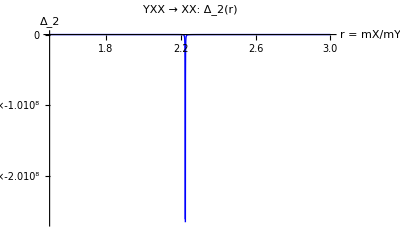

```mathematica
(* Numerical table *)
Print["\n===== Delta_2(r) for selected mass ratios ====="];
Print[PaddedForm[
  TableForm[
   Table[{r0, N[Delta2 /. r -> r0, 8]}, {r0, {1.5,2, 3, 5, 7, 10, 15, 20, 50, 100}}],
   TableHeadings -> {None, {"r = mX/mY", "Delta_2"}}], {8, 4}]];

(* Plot *)
Plot[Delta2, {r, 1.5, 3},
 PlotRange -> All,
 ScalingFunctions -> {"Linear", "Linear"},
 AxesLabel -> {"r = mX/mY", "Δ_2"},
 PlotLabel -> "YXX → XX:  Δ_2(r)",
 PlotStyle -> {Thick, Blue}]
```